```mathematica
Ln=4;
```

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

Ordered Entropy

```mathematica
EN[L_,p_]:=-(Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

Cyclic Entropy

```mathematica
ENC[p_]:=-(Log[1-p]+p/(1-p)*Log[p])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

```mathematica
T1=Flatten[{Evaluate@Table[P1[i,h[0.5]],{i,0,3}],P2[Ln,h[0.5]]}];
T2=Flatten[{Evaluate@Table[P1[i,h[2]],{i,0,3}],P2[Ln,h[2]]}];
T3=N[Flatten[{Evaluate@Table[P1[i,h[20]],{i,0,3}],P2[Ln,h[20]]}]]
```

{0.047619,0.0453515,0.0431919,0.0411351,0.822702}

```mathematica
Sum[T1[[i]],{i,1,5}]
Sum[T2[[i]],{i,1,5}]
Sum[T3[[i]],{i,1,5}]
```

1.

1

1.

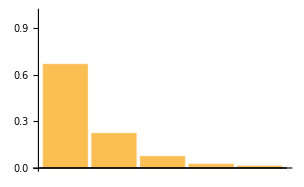

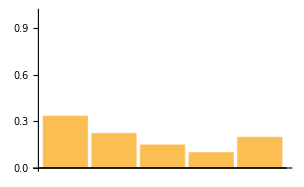

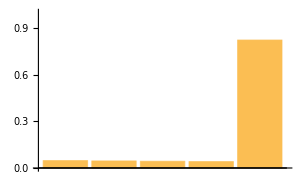

```mathematica
BarChart[T1, PlotRange->{0,1}]
BarChart[T2, PlotRange->{0,1}]
BarChart[T3, PlotRange->{0,1}]
```